## Lesson

Repeatedly apply a function n times:

```mathematica
Nest[f,x,3]
```

f[f[f[x]]]

Nest a function gradually n times:

```mathematica
NestList[f,x,3]
```

{x,f[x],f[f[x]],f[f[f[x]]]}

Make a graph edge each time the function is applied:

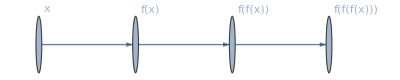

```mathematica
NestGraph[f,x,3,VertexLabels->Automatic]
```

## Questions

Q1. Make a list of the results of nesting Blur up to 10 times, starting with a rasterized size-30 “X”.

```mathematica
NestList[Blur,Rasterize[Style["X",30]],10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Q2. Start with x, then make a list by nestedly applying Framed up to 10 times, using a random background colour each time.

```mathematica
NestList[Style[Framed[#],RandomColor[]]&,x,10]
```

{x,x,x,x,x,x,x,x,x,x,x}

Q3. Start with a size-50 “A”, then make a list of nestedly applying a frame and a random rotation 5 times.

```mathematica
NestList[Rotate[Framed[#],RandomReal[360]°]&,Rasterize[Style["A",50]],5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Q4. Make a line plot of 100 iterations of the logistic map iteration 4 #(1-#)&, starting from 0.2.

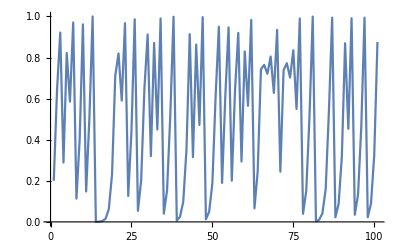

```mathematica
ListLinePlot[NestList[4 #(1-#)&,0.2,100]]
```

Q5. Find the numerical value of the result from 30 iterations of 1+1/#& starting from 1.

```mathematica
N[NestList[1+1/#&,1,30]]
```

{1.,2.,1.5,1.66667,1.6,1.625,1.61538,1.61905,1.61765,1.61818,1.61798,1.61806,1.61803,1.61804,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803}

Q6. Create a list of the first 10 powers of 3 (starting at 0) by nested multiplication.

```mathematica
NestList[#+3&,0,10]
```

{0,3,6,9,12,15,18,21,24,27,30}

Q7. Make a list of the result of nesting the (Newton’s method) function (#+2/#)/2& up to 5 times starting from 1.0, and then subtract from √2 all the results.

```mathematica
NestList[(#+2/#)/2&,1.0,5]-√2
```

{-0.414214,0.0857864,0.0024531,2.1239×10^-6,1.59472×10^-12,-2.22045×10^-16}

Q8. Make graphics of a 1000-step 2D random walk which starts at {0, 0}, and in which at each step a pair of random numbers between −1 and +1 are added to the coordinates.

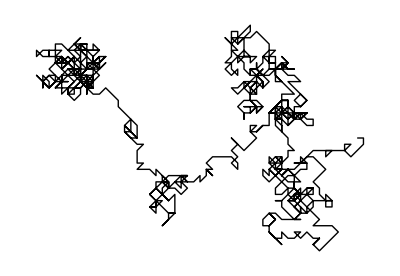

```mathematica
Graphics[Line[NestList[#+RandomInteger[{-1,1},2]&,{0,0},1000]]]
```

Q9. Make an array plot of 50 steps of Pascal’s triangle modulo 2 by starting from {1} and nestedly joining {0} at the beginning and at the end, and adding these results together modulo 2.

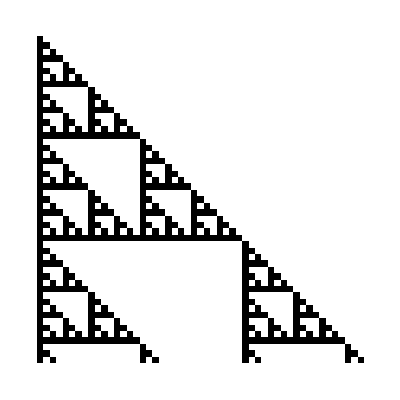

```mathematica
ArrayPlot[NestList[Mod[Join[{0},#]+Join[#,{0}],2]&,{1},50]]
```

Q10. Generate a graph by starting from 0, then nestedly 10 times connecting each node with value n to ones with values n+1 and 2n.

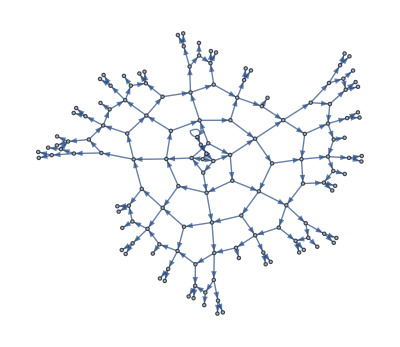

```mathematica
NestGraph[{#+1,2#}&,0,10]
```

Q11. Generate a graph obtained by nestedly finding bordering countries starting from the United States, and going 4 iterations.

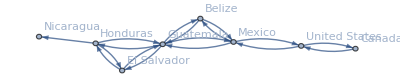

```mathematica
NestGraph[#["BorderingCountries"]&,Entity["Country","UnitedStates"],4,VertexLabels->Automatic]
```

## Extended Questions

+Q1. Make a line plot of 100 iterations of linear congruential function Mod[59#, 101]&, starting from 1.

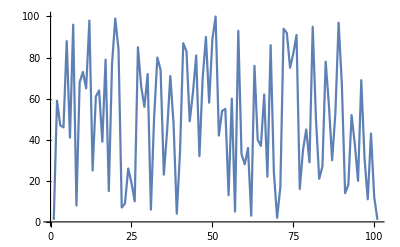

```mathematica
ListLinePlot[NestList[Mod[59#,101]&,1,100]]
```

+Q2. Create a list of 5 power towers of 2, i.e. 2^2^2...^2 n times, with n from 0 to 4.

```mathematica
NestList[2^#&,1,4]
```

{1,2,4,16,65536}

+Q3. Create a list of 20 power towers of 1.2, i.e. 1.2^1.2^...^1.2 n times, with n from 0 to 19.

```mathematica
NestList[1.2^#&,1,19]
```

{1,1.2,1.24456,1.25472,1.25704,1.25758,1.2577,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773}

+Q4. Generate a list of the numerical values obtained by up to 10 nestings of the function Sqrt[1+#]&.

```mathematica
N[NestList[Sqrt[1+#]&,1,10]]
```

{1.,1.41421,1.55377,1.59805,1.61185,1.61612,1.61744,1.61785,1.61798,1.61802,1.61803}

+Q5. Make graphics of a 1000-step 3D random walk which starts at {0, 0, 0}, and in which at each step a triple of random numbers between −1 and +1 are added to the coordinates.

```mathematica
Graphics3D[Line[NestList[#+RandomInteger[{-1,1},3]&,{0,0,0},1000]]]
```

-Graphics3D-